```mathematica
ClearAll
```

ClearAll

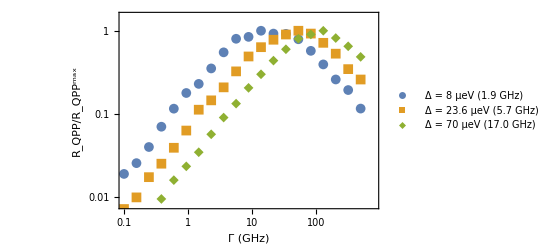

```mathematica
(* Plot of numerical data of quasiparticle pair excitation rates versus TLF transition frequency for different values of the topological gap *)

(*  *)
(* triples are: Gamma (GHz), R_QPP (pairs/s) for specific numerical conditions *)
(* This program plots a scaled R_QPP (scaled to the maximum value as a function of Gamma achieved at each gap).  The scaled rate is plotted because the quasiparticle excitation rate depends on the Fermi velocity, which depends both on the superconducting gap and the superconducting coherence length.  We focus on the behavior as a function of the magnitude of the superconducting gap by plotting the scaled quantity, which does not depend on Fermi velocity.   *)


(* 0.6 GHz *)
data600MHz={
{0.1,0.455656602,0.003109315},
{0.156560656,0.367179382,0.00309722},
{0.245112389,0.587248209,0.003676147},
{0.383749564,0.966206470,0.004704837},
{0.600800835,1.649775773,0.010594913},
{0.940617727,2.536955271,0.00764006},
{1.472637281,2.522571098,0.009614552},
{2.305570585,2.847785269,0.010956361},
{3.609616427,2.833628933,0.011314518},
{5.65123915,2.994376304,0.00702346},
{8.847617075,2.894130697,0.009176739},
{13.85188731,2.045020434,0.004274637},
{21.68660562,1.723509629,0.002595254},
{33.95269198,1.149510866,0.003567702},
{53.15655722,0.882374185,0.002325679},
{83.22225458,0.552129591,0.00098282},
{130.2933075,0.424439992,0.001050162},
{203.9880567,0.282980206,0.000601788},
{319.3650394,0.195898982,0.000727282},
{500,0.125074255,0.000249221}
};

data1900MHz={
{0.1,0.090122371,0.000271531},
{0.156560656,0.121529995,0.000296141},
{0.245112389,0.190065802,0.000543017},
{0.383749564,0.333560442,0.00088289},
{0.600800835,0.550107981 ,0.000893462},
{0.940617727, 0.849377448 ,0.00156258},
{1.472637281, 1.093131351, 0.001675231},
{2.305570585 ,1.678250201 ,0.002237932},
{3.609616427 ,2.621111134 ,0.005907007},
{5.65123915 ,3.817717985,0.010284815},
{8.847617075,4.025294147,0.007820998},
{13.85188731,4.76850257,0.008528522},
{21.68660562 ,4.407648767 ,0.007354758},
{33.95269198, 4.374548177 ,0.00659981},
{53.15655722 ,3.768004097 ,0.008480341},
{83.22225458 ,2.732403582 ,0.006687718},
{130.2933075 ,1.875457372 ,0.002232972},
{203.9880567 ,1.235866006 ,0.001973669},
{319.3650394 ,0.921613875 ,0.00138073},
{500 ,0.551478859 ,0.000928502}
};

data5700MHz={
{0.1, 0.04963862, 0.000171305},
{0.156560656 ,0.068516911,0.0000559},
{0.245112389 ,0.120038049 ,0.000354709},
{0.383749564 ,0.174361948 ,0.000398218},
{0.600800835 ,0.271042308 ,0.000450410},
{0.940617727, 0.436868146 ,0.000611461},
{1.472637281 ,0.778727548 ,0.000703711},
{2.305570585 ,1.009092094 ,0.001134309},
{3.609616427, 1.447119339,0.002304726},
{5.65123915 ,2.252927395,0.002722410},
{8.847617075, 3.405706656 ,0.005841350},
{13.85188731, 4.406251159 ,0.003221283},
{21.68660562 ,5.415464725, 0.003744463},
{33.95269198 ,6.260849535 ,0.006359527},
{53.15655722, 6.947682513 ,0.006443239},
{83.22225458 ,6.424699632 ,0.003774696},
{130.2933075, 4.972851712, 0.006004989},
{203.9880567 ,3.680401061 ,0.006689488},
{319.3650394 ,2.39788584 ,0.002492088},
{500 ,1.798485807 ,0.002016481}
};

data17000MHz={
{0.1 ,0.015922119 ,0.00004151},
{0.156560656 ,0.031270688, 0.00008493},
{0.245112389 ,0.039139403 ,0.00007215},
{0.383749564 ,0.066882076 ,0.00012966},
{0.600800835 ,0.112647808 ,0.00013755},
{0.940617727 ,0.165131065 ,0.00018795},
{1.472637281 ,0.244193408 ,0.00024150},
{2.305570585 ,0.401554237 ,0.00053848},
{3.609616427 ,0.638391597 ,0.00064076},
{5.65123915 ,0.939489056 ,0.00126617},
{8.847617075 ,1.454127515 ,0.00115456},
{13.85188731 ,2.119486622 ,0.00195532},
{21.68660562 ,3.094438899 ,0.00443616},
{33.95269198 ,4.23873344 ,0.00387842},
{53.15655722 ,5.674180316 ,0.00372208},
{83.22225458 ,6.399789997 ,0.00393211},
{130.2933075 ,7.081120133 ,0.00322572},
{203.9880567 ,5.785376142 ,0.00282981},
{319.3650394 ,4.602363248 ,0.00350858},
{500 ,3.43292988 ,0.00331796}
};

data51100MHz={
{0.1, 0.005889555 ,0.0000148},
{0.156560656, 0.008442441, 0.0000190},
{0.245112389 ,0.014895339 ,0.0000301},
{0.383749564 ,0.023145204 ,0.0000339},
{0.600800835 ,0.035614098 ,0.0000490},
{0.940617727 ,0.053096153 ,0.0000573},
{1.472637281 ,0.087268955 ,0.0000667},
{2.305570585 ,0.136481231 ,0.0001196},
{3.609616427 ,0.206010854 ,0.0001450},
{5.65123915 ,0.339276892 ,0.0002983},
{8.847617075 ,0.46251922 ,0.0002942},
{13.85188731 ,0.789021186 ,0.0008306},
{21.68660562 ,1.219864935 ,0.0007262},
{33.95269198 ,1.773039261 ,0.0016948},
{53.15655722 ,2.617455479 ,0.0019613},
{83.22225458 ,3.639983896 ,0.0018627},
{130.2933075 ,4.335733279 ,0.0029702},
{203.9880567 ,5.050193563 ,0.0030567},
{319.3650394 ,5.131987638 ,0.0040885},
{500 ,4.288767228 ,0.0028961}
};

maxVal600MHz=Max[data600MHz[[All,2]]];
maxVal1900MHz=Max[data1900MHz[[All,2]]];
maxVal5700MHz=Max[data5700MHz[[All,2]]];
maxVal17000MHz=Max[data17000MHz[[All,2]]];
maxVal51100MHz=Max[data51100MHz[[All,2]]];

newdata600MHz=MapAt[#/maxVal600MHz&,data600MHz,{All,2}];
newdata1900MHz=MapAt[#/maxVal1900MHz&,data1900MHz,{All,2}];
newdata5700MHz=MapAt[#/maxVal5700MHz&,data5700MHz,{All,2}];
newdata17000MHz=MapAt[#/maxVal17000MHz&,data17000MHz,{All,2}];
newdata51100MHz=MapAt[#/maxVal51100MHz&,data51100MHz,{All,2}];

ListLogLogPlot[{
{#1,#2}&@@@newdata1900MHz,
{#1,#2}&@@@newdata5700MHz,
{#1,#2}&@@@newdata17000MHz},PlotRange->{{0.1,800},{0.008,1.5}},PlotMarkers->{Automatic,10},PlotLegends->Placed[{"Δ = 8 μeV (1.9 GHz)","Δ = 23.6 μeV (5.7 GHz)","Δ = 70 μeV (17.0 GHz)"},{0.72,0.23}],
Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->13.5,FontFamily->"Helvetica"},FrameLabel->{"Γ (GHz)","R_QPP/R_QPP^max",None,None},
FrameTicks->{{{0.01,0.1,1},None},{{0.1,1,10,100},None}}
]
```